# ColorData.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\ColorData.nb

## general

par

ColorData["scheme"][par] 或 ColorData["scheme", par]
给出指定颜色方案中对应于参数值 par 的 RGBColor 对象.

```mathematica
ColorData["SiennaTones"]
ColorData["SiennaTones"][0.7]
```

ColorDataFunction[…]

RGBColor[0.9219818, 0.7520014, 0.5468027999999999]

默认情况下

默认情况下，颜色梯度有一个范围从0到1的单一参数.

逆向排序

ColorData[{"gradient","Reverse"}] 给出范围在0和1之间的颜色梯度，其中对颜色的逆向排序.

```mathematica
ColorData[{"SiennaTones","Reverse"}]
ColorData[{"SiennaTones","Reverse"}][0.7]
```

ColorDataFunction[…]

RGBColor[0.8185106000000001, 0.40547180000000005, 0.14248416000000003]

min 和 max

ColorData[{"gradient",{min,max}}] 给出范围在 min 和 max 之间的颜色梯度.

```mathematica
ColorData["LakeColors"]
ColorData[{"LakeColors",{0,0.5}}]
```

ColorDataFunction[…]

ColorDataFunction[…]

索引

ColorData[n,…] 使用第n个索引的调色板.

"Indexed",用连续整数索引的颜色

```mathematica
ColorData[2,"Name"]
ColorData[2]
```

2

ColorDataFunction[…]

属性

梯度是一个连续颜色函数，它适用于 ColorFunction:

```mathematica
ColorData[{"LakeColors",{0,0.5}},"ColorFunction"]
```

ColorDataFunction[…]

```mathematica
ColorData[{"LakeColors",{0,0.5}},"ColorList"]
```

Missing[NotApplicable]

```mathematica
ColorData[{"LakeColors",{0,0.5}},"ColorRules"]
```

Missing[NotApplicable]

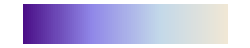

```mathematica
ColorData[{"LakeColors",{0,0.5}},"Image"]
```

```mathematica
ColorData[{"LakeColors",{0,0.5}},"Name"]
```

lake colors

```mathematica
ColorData[{"LakeColors",{0,0.5}},"Panel"]
```

-Graphics-

```mathematica
ColorData[{"LakeColors",{0,0.5}},"ParameterCount"]
```

1

```mathematica
ColorData[{"LakeColors",{0,0.5}},"Range"]
```

{0,0.5}

```mathematica
ColorData[{"LakeColors",{0,0.5}},{"Range",1}]
```

{0,1}

```mathematica
ColorData[{"LakeColors",{0,0.5}},{"Range",2}]
```

Missing[NotApplicable]

## scenario and schemes

获得集合的列表：

```mathematica
ColorData[]
```

{Gradients,Indexed,Named,Physical}

求出属于每个集合的方案：

归一化的连续颜色梯度

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

用连续整数索引的颜色

```mathematica
ColorData["Indexed"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113}

命名颜色的集合

```mathematica
ColorData["Named"]
```

{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe}

物理参数确定的颜色

```mathematica
ColorData["Physical"]
```

{BlackBodySpectrum,HypsometricTints,VisibleSpectrum}

```mathematica
ColorData["Properties"]
```

{AlternateNames,ColorFunction,ColorList,ColorRules,Image,Name,Panel,ParameterCount,Range,StandardName}

## 例子

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2,2},ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

-Graphics3D-

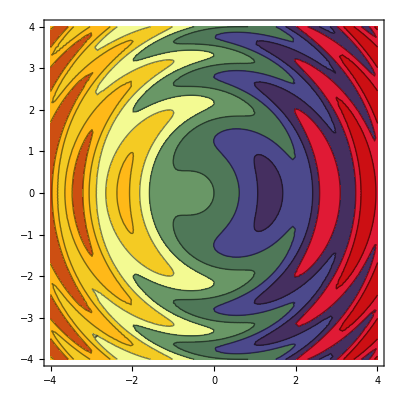

```mathematica
ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[35,"ColorList"]]
```

## 属性

examples

```mathematica
ColorData[38,"ColorList"]
```

{RGBColor[0.5686274509803921, 0.2980392156862745, 0.1450980392156863],RGBColor[0.7058823529411765, 0.6980392156862745, 0.4980392156862745],RGBColor[0.6509803921568628, 0.7607843137254902, 0.22745098039215686],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.8235294117647058, 0.8941176470588236, 0.9490196078431372],RGBColor[0.22745098039215686, 0.19215686274509805, 0.4],RGBColor[0.5019607843137255, 0.23921568627450981, 0.4470588235294118],RGBColor[0.6705882352941176, 0.12941176470588237, 0.22745098039215686]}

```mathematica
Short[ColorData["Atoms","ColorList"]]
```

{RGBColor[0.65, 0.7, 0.7],RGBColor[0.836713, 1., 1.],RGBColor[0.799435, 0.543572, 0.997559],RGBColor[0.770565, 0.964309, 0.0442359],RGBColor[1., 0.709804, 0.709804],RGBColor[0.4, 0.4, 0.4],RGBColor[0.291989, 0.437977, 0.888609],RGBColor[0.800498, 0.201504, 0.192061],RGBColor[0.578462, 0.85539, 0.408855],RGBColor[0.677263, 0.928423, 0.955287],RGBColor[0.658708, 0.492173, 0.842842],RGBColor[0.628274, 0.850553, 0.0782731],RGBColor[0.8913, 0.631904, 0.627399],RGBColor[0.941176, 0.784314, 0.627451],RGBColor[1., 0.501961, 0],RGBColor[0.90443, 0.97015, 0.13504],RGBColor[0.412698, 0.932689, 0.166398],RGBColor[0.546138, 0.844244, 0.892092],RGBColor[0.534026, 0.420729, 0.705621],RGBColor[0.480072, 0.744591, 0.0955222],RGBColor[0.901961, 0.901961, 0.901961],RGBColor[0.74902, 0.760784, 0.780392],RGBColor[0.65098, 0.65098, 0.670588],RGBColor[0.541176, 0.6, 0.780392],«70»,RGBColor[0.52326, 0.469458, 0.735517],RGBColor[0.549486, 0.433847, 0.697999],RGBColor[0.573624, 0.399845, 0.661808],RGBColor[0.595673, 0.367454, 0.626942],RGBColor[0.615633, 0.336672, 0.593404],RGBColor[0.633505, 0.307499, 0.561191],RGBColor[0.649288, 0.279937, 0.530305],RGBColor[0.662982, 0.253984, 0.500746],RGBColor[0.674588, 0.22964, 0.472513],RGBColor[0.684106, 0.206907, 0.445606],RGBColor[0.691534, 0.185783, 0.420025],RGBColor[0.696874, 0.166269, 0.395772],RGBColor[0.700126, 0.148365, 0.372844],RGBColor[0.701289, 0.13207, 0.351243],RGBColor[0.700363, 0.117385, 0.330968],RGBColor[0.697348, 0.10431, 0.31202],RGBColor[0.692245, 0.0928444, 0.294398],RGBColor[0.685054, 0.0829886, 0.278102],RGBColor[0.675773, 0.0747426, 0.263133],RGBColor[0.664405, 0.0681063, 0.249491],RGBColor[0.650947, 0.0630797, 0.237174],RGBColor[0.635401, 0.0596628, 0.226184],RGBColor[0.635401, 0.0596628, 0.226184],RGBColor[0.635401, 0.0596628, 0.226184]}

```mathematica
ColorData[42,"ColorRules"]
```

{1→RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392],2→RGBColor[0.7333333333333333, 0.6666666666666666, 0.5411764705882353],3→RGBColor[0.5843137254901961, 0.5333333333333333, 0.4117647058823529],4→RGBColor[0.6862745098039216, 0.6470588235294118, 0.27450980392156865]}

```mathematica
Short[ColorData["Legacy","ColorRules"],3]
```

{AliceBlue→RGBColor[0.941206, 0.972503, 1.],AlizarinCrimson→RGBColor[0.889996, 0.149998, 0.209998],Antique→RGBColor[0.980575, 0.92233, 0.844661],Apricot→RGBColor[1., 0.340007, 0.129994],«185»,YellowBrown→RGBColor[0.86, 0.58, 0.44],YellowGreen→RGBColor[0.6039, 0.803903, 0.196097],YellowOchre→RGBColor[0.889996, 0.509995, 0.089999],Zinc→RGBColor[0.990005, 0.97, 1.]}

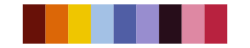

```mathematica
ColorData[22,"Image"]
```

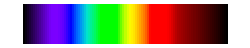

```mathematica
ColorData["VisibleSpectrum","Image"]
```

```mathematica
ColorData["HTML","Name"]
```

HTML

```mathematica
ColorData["HTML","StandardName"]
```

HTML

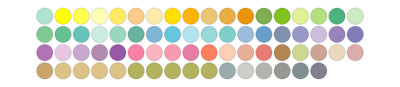

```mathematica
ColorData["GeologicAges","Panel"]
```

```mathematica
ColorData[12,"Range"]
```

{1,10,1}

```mathematica
ColorData["VisibleSpectrum","Range"]
```

{380,750}

属性值

属性值可以是任意有效的 Mathematica 表达式：

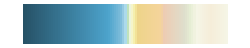

```mathematica
ColorData["HypsometricTints","Image"]
```

```mathematica
ColorData[37,"ColorRules"]
Take[ColorData[37,"ColorRules"],3]
```

{1→RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],2→RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],3→RGBColor[1., 0.5568627450980392, 0.3215686274509804],4→RGBColor[1., 0.807843137254902, 0.4627450980392157],5→RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785],6→RGBColor[0.6588235294117647, 0.596078431372549, 0.27058823529411763],7→RGBColor[0.9294117647058824, 0.9058823529411765, 0.7803921568627451],8→RGBColor[0.8117647058823529, 0.7607843137254902, 0.47843137254901963],9→RGBColor[0.6588235294117647, 0.7803921568627451, 0.9411764705882353],10→RGBColor[0.4235294117647059, 0.6039215686274509, 0.8431372549019608],11→RGBColor[0.2, 0.41568627450980394, 0.7019607843137254]}

{1→RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],2→RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],3→RGBColor[1., 0.5568627450980392, 0.3215686274509804]}

当应用的值在一个特定的范围内时，ColorDataFunction 返回 RGB 颜色：

```mathematica
ColorData["GrayYellowTones"][.5]
```

RGBColor[0.6918275, 0.7071305, 0.7518994999999999]

```mathematica
ColorData["ThermometerColors"]
```

ColorDataFunction[…]

巧妙范例

```mathematica
ReliefPlot[Table[RandomReal[](Sin[x+y^2]+Sin[x^2+3y]),{x,-3,3,.01},{y,-3,3,.01}],ColorFunction->ColorData["SouthwestColors"]]
```

-Graphics-

所有梯度的缩略图：

```mathematica
Grid[Partition[Show[ColorData[#,"Image"],ImageSize->110]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |